```mathematica
SetDirectory[NotebookDirectory[]];

gfactor=Import["g-factor","TSV"];
energy=Import["energies","TSV"];
```

```mathematica
gfactor[[1]][[2]]
```

10.6152

```mathematica
energy[[1]][[3]]
```

11.8652

```mathematica
gfactor//Dimensions
energy//Dimensions
```

{10,5}

{10,21}

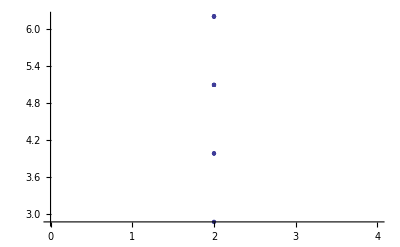

```mathematica
i=2;ListPlot[Table[{i,energy[[i]][[j]]},{j,1,21}]]
```

```mathematica
h^2/(0.067*10^-30*(32*10^-9)^2)10^19/1.6
```

0.000910972

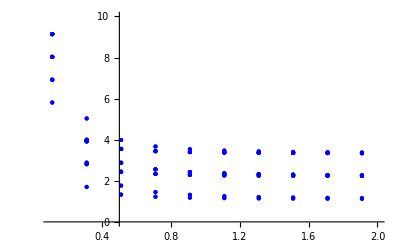

```mathematica
a=ListPlot[Table[Table[{(11+20(i-1))*10^-9,energy[[i]][[j]]},{i,1,10}],{j,1,20}],PlotRange->{{10^-8,2*10^-7},{0,10}},PlotStyle->Blue]
```

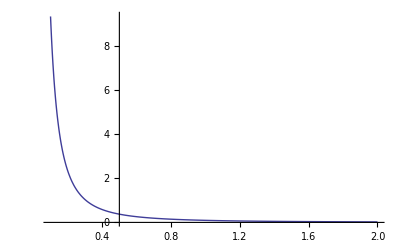

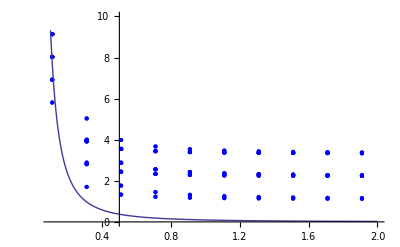

```mathematica
h=10^-34;b=Plot[(h^2/(0.067*10^-30 x^2))*10^19/1.6*10^3,{x,10*10^-9,200*10^-9},PlotRange->All]
Show[{a,b}]
```

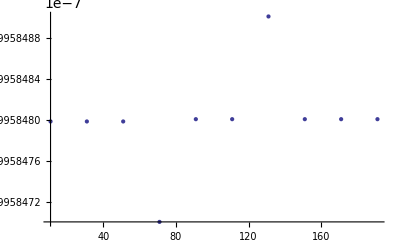

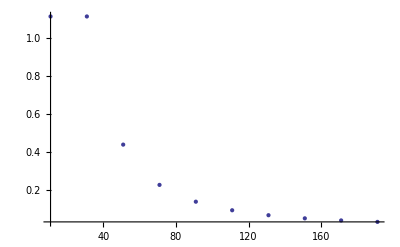

-Graphics-

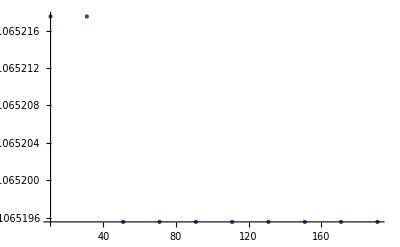

-Graphics-

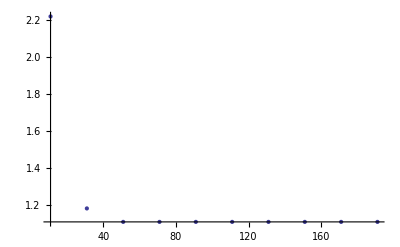

-Graphics-

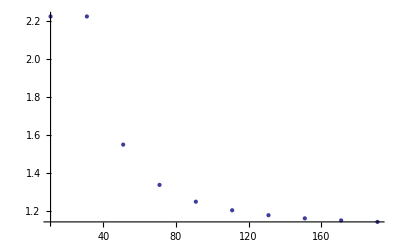

-Graphics-

-Graphics-

-Graphics-

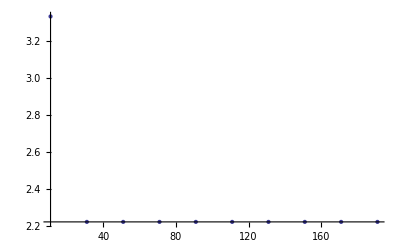

-Graphics-

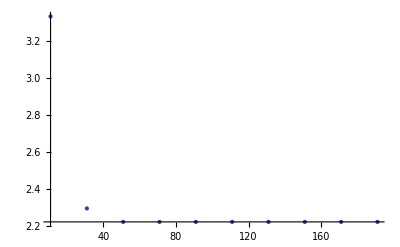

-Graphics-

-Graphics-

-Graphics-

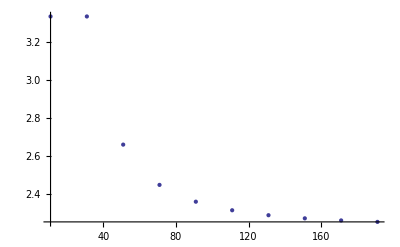

-Graphics-

-Graphics-

```mathematica
ListPlot[Table[{11+20(i-1),energy[[i]][[2]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[3]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[4]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[5]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[6]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[7]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[8]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[9]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[10]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[11]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[12]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[13]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]

ListPlot[Table[{11+20(i-1),energy[[i]][[14]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[15]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[16]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[17]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[18]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[19]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[20]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
ListPlot[Table[{11+20(i-1),energy[[i]][[21]]-energy[[i]][[1]]},{i,1,10}],PlotRange->All]
```

```mathematica
gfactor
```

{{11.,5.81027,5.81027,2.19959×10^-7,0.38},{31.,1.70238,1.70238,2.19959×10^-7,0.38},{51.,1.32928,1.32928,2.19959×10^-7,0.38},{71.,1.22346,1.22346,2.19959×10^-7,0.38},{91.,1.17932,1.17932,2.19959×10^-7,0.38},{111.,1.15681,1.15681,2.19959×10^-7,0.38},{131.,1.14379,1.14379,2.19959×10^-7,0.38},{151.,1.13559,1.13559,2.19959×10^-7,0.38},{171.,1.1301,1.1301,2.19959×10^-7,0.38},{191.,1.12624,1.12624,2.19959×10^-7,0.38}}

```mathematica
energy
```

{{5.81027,5.81027,6.92092,6.92092,6.92092,6.92092,8.03157,8.03157,8.03157,8.03157,8.03157,8.03157,9.14223,9.14223,9.14223,9.14223,9.14223,9.14223,9.14223,9.14223,+5.81027059808228e+00 +5.81027081804076e+00 +6.92092255343186e+00 +6.92092255343220e+00 +6.92092277339026e+00 +6.92092277339071e+00 +8.03157416712175e+00 +8.03157429722056e+00 +8.03157438708016e+00 +8.03157451717906e+00 +8.03157463887307e+00 +8.03157485883149e+00 +9.14222644113477e+00 +9.14222644113484e+00 +9.14222666109304e+00 +9.14222666109331e+00 +9.14222822036243e+00 +9.14222822036248e+00 +9.14222844032071e+00 +9.14222844032103e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.70238,1.70238,2.81304,2.81304,2.81304,2.81304,2.88585,2.88585,3.92369,3.92369,3.92369,3.92369,3.92369,3.92369,3.9965,3.9965,3.9965,3.9965,5.03434,5.03434,+1.70238331514979e+00 +1.70238353510827e+00 +2.81303527049955e+00 +2.81303527049958e+00 +2.81303549045804e+00 +2.81303549045805e+00 +2.88584608013666e+00 +2.88584630009514e+00 +3.92368688418915e+00 +3.92368701428806e+00 +3.92368710414761e+00 +3.92368723424651e+00 +3.92368735594046e+00 +3.92368757589897e+00 +3.99649803548641e+00 +3.99649803548645e+00 +3.99649825544490e+00 +3.99649825544492e+00 +5.03433915820228e+00 +5.03433937816075e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.32928,1.32928,1.76654,1.76654,2.43993,2.43993,2.43993,2.43993,2.87719,2.87719,2.87719,2.87719,3.55058,3.55058,3.55058,3.55058,3.55058,3.55059,3.98784,3.98784,+1.32928086728138e+00 +1.32928108723986e+00 +1.76653873653139e+00 +1.76653895648983e+00 +2.43993282263110e+00 +2.43993282263120e+00 +2.43993304258954e+00 +2.43993304258970e+00 +2.87719069188109e+00 +2.87719069188112e+00 +2.87719091183956e+00 +2.87719091183961e+00 +3.55058443632067e+00 +3.55058456641961e+00 +3.55058465627915e+00 +3.55058478637807e+00 +3.55058490807199e+00 +3.55058512803050e+00 +3.98784230557064e+00 +3.98784243566955e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.22346,1.22346,1.44907,1.44907,2.33411,2.33411,2.33411,2.33411,2.55972,2.55972,2.55972,2.55972,3.44476,3.44476,3.44476,3.44476,3.44476,3.44476,3.67037,3.67037,+1.22345769742200e+00 +1.22345791738047e+00 +1.44906922695321e+00 +1.44906944691161e+00 +2.33410965277170e+00 +2.33410965277176e+00 +2.33410987273018e+00 +2.33410987273028e+00 +2.55972118230284e+00 +2.55972118230297e+00 +2.55972140226132e+00 +2.55972140226142e+00 +3.44476126646138e+00 +3.44476139656024e+00 +3.44476148641974e+00 +3.44476161651870e+00 +3.44476173821260e+00 +3.44476195817121e+00 +3.67037279599244e+00 +3.67037292609140e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.17932,1.17932,1.31666,1.31666,2.28997,2.28997,2.28997,2.28997,2.42731,2.42731,2.42731,2.42731,3.40063,3.40063,3.40063,3.40063,3.40063,3.40063,3.53796,3.53796,+1.17932164199292e+00 +1.17932186195140e+00 +1.31666106066603e+00 +1.31666128062455e+00 +2.28997359734267e+00 +2.28997359734274e+00 +2.28997381730120e+00 +2.28997381730122e+00 +2.42731301601577e+00 +2.42731301601584e+00 +2.42731323597427e+00 +2.42731323597430e+00 +3.40062521103231e+00 +3.40062534113113e+00 +3.40062543099075e+00 +3.40062556108965e+00 +3.40062568278360e+00 +3.40062590274212e+00 +3.53796462970534e+00 +3.53796475980430e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.15681,1.15681,1.24911,1.24911,2.26746,2.26746,2.26746,2.26746,2.35976,2.35976,2.35976,2.35976,3.37811,3.37811,3.37811,3.37811,3.37811,3.37811,3.47042,3.47042,+1.15680515629716e+00 +1.15680537625564e+00 +1.24911160357878e+00 +1.24911182353728e+00 +2.26745711164689e+00 +2.26745711164694e+00 +2.26745733160538e+00 +2.26745733160541e+00 +2.35976355892850e+00 +2.35976355892854e+00 +2.35976377888697e+00 +2.35976377888704e+00 +3.37810872533655e+00 +3.37810885543537e+00 +3.37810894529490e+00 +3.37810907539389e+00 +3.37810919708781e+00 +3.37810941704636e+00 +3.47041517261814e+00 +3.47041530271696e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.14379,1.14379,1.21006,1.21006,2.25444,2.25444,2.25444,2.25444,2.32071,2.32071,2.32071,2.32071,3.36509,3.36509,3.36509,3.36509,3.36509,3.36509,3.43136,3.43136,+1.14378833949995e+00 +1.14378855945844e+00 +1.21006115318717e+00 +1.21006137314566e+00 +2.25444029484974e+00 +2.25444029484976e+00 +2.25444051480822e+00 +2.25444051480822e+00 +2.32071310853689e+00 +2.32071310853690e+00 +2.32071332849538e+00 +2.32071332849539e+00 +3.36509190853924e+00 +3.36509203863818e+00 +3.36509212849772e+00 +3.36509225859665e+00 +3.36509238029061e+00 +3.36509260024903e+00 +3.43136472222643e+00 +3.43136485232532e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.13559,1.13559,1.18547,1.18547,2.24624,2.24624,2.24624,2.24624,2.29612,2.29612,2.29612,2.29612,3.3569,3.3569,3.3569,3.3569,3.3569,3.3569,3.40678,3.40678,+1.13559179900584e+00 +1.13559201896432e+00 +1.18547153170479e+00 +1.18547175166328e+00 +2.24624375435561e+00 +2.24624375435562e+00 +2.24624397431410e+00 +2.24624397431410e+00 +2.29612348705457e+00 +2.29612348705458e+00 +2.29612370701308e+00 +2.29612370701309e+00 +3.35689536804517e+00 +3.35689549814407e+00 +3.35689558800362e+00 +3.35689571810250e+00 +3.35689583979653e+00 +3.35689605975503e+00 +3.40677510074413e+00 +3.40677523084301e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.1301,1.1301,1.16899,1.16899,2.24075,2.24075,2.24075,2.24075,2.27965,2.27965,2.27965,2.27965,3.3514,3.3514,3.3514,3.3514,3.3514,3.3514,3.3903,3.3903,+1.13009907586726e+00 +1.13009929582574e+00 +1.16899336228901e+00 +1.16899358224752e+00 +2.24075103121700e+00 +2.24075103121704e+00 +2.24075125117551e+00 +2.24075125117552e+00 +2.27964531763881e+00 +2.27964531763881e+00 +2.27964553759728e+00 +2.27964553759730e+00 +3.35140264490657e+00 +3.35140277500548e+00 +3.35140286486498e+00 +3.35140299496394e+00 +3.35140311665790e+00 +3.35140333661640e+00 +3.39029693132838e+00 +3.39029706142723e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{1.12624,1.12624,1.15741,1.15742,2.23689,2.23689,2.23689,2.23689,2.26807,2.26807,2.26807,2.26807,3.34754,3.34754,3.34754,3.34754,3.34754,3.34754,3.37872,3.37872,+1.12623960694867e+00 +1.12623982690715e+00 +1.15741495553324e+00 +1.15741517549174e+00 +2.23689156229842e+00 +2.23689156229843e+00 +2.23689178225689e+00 +2.23689178225693e+00 +2.26806691088298e+00 +2.26806691088298e+00 +2.26806713084147e+00 +2.26806713084148e+00 +3.34754317598798e+00 +3.34754330608688e+00 +3.34754339594642e+00 +3.34754352604533e+00 +3.34754364773927e+00 +3.34754386769782e+00 +3.37871852457253e+00 +3.37871865467144e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 }}

```mathematica
Table[{11+20(i-1),energy[[i]][[21]]-energy[[i]][[1]]},{i,1,10}]
```

{{11,-5.81027++5.81027059808228e+00 +5.81027081804076e+00 +6.92092255343186e+00 +6.92092255343220e+00 +6.92092277339026e+00 +6.92092277339071e+00 +8.03157416712175e+00 +8.03157429722056e+00 +8.03157438708016e+00 +8.03157451717906e+00 +8.03157463887307e+00 +8.03157485883149e+00 +9.14222644113477e+00 +9.14222644113484e+00 +9.14222666109304e+00 +9.14222666109331e+00 +9.14222822036243e+00 +9.14222822036248e+00 +9.14222844032071e+00 +9.14222844032103e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{31,-1.70238++1.70238331514979e+00 +1.70238353510827e+00 +2.81303527049955e+00 +2.81303527049958e+00 +2.81303549045804e+00 +2.81303549045805e+00 +2.88584608013666e+00 +2.88584630009514e+00 +3.92368688418915e+00 +3.92368701428806e+00 +3.92368710414761e+00 +3.92368723424651e+00 +3.92368735594046e+00 +3.92368757589897e+00 +3.99649803548641e+00 +3.99649803548645e+00 +3.99649825544490e+00 +3.99649825544492e+00 +5.03433915820228e+00 +5.03433937816075e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{51,-1.32928++1.32928086728138e+00 +1.32928108723986e+00 +1.76653873653139e+00 +1.76653895648983e+00 +2.43993282263110e+00 +2.43993282263120e+00 +2.43993304258954e+00 +2.43993304258970e+00 +2.87719069188109e+00 +2.87719069188112e+00 +2.87719091183956e+00 +2.87719091183961e+00 +3.55058443632067e+00 +3.55058456641961e+00 +3.55058465627915e+00 +3.55058478637807e+00 +3.55058490807199e+00 +3.55058512803050e+00 +3.98784230557064e+00 +3.98784243566955e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{71,-1.22346++1.22345769742200e+00 +1.22345791738047e+00 +1.44906922695321e+00 +1.44906944691161e+00 +2.33410965277170e+00 +2.33410965277176e+00 +2.33410987273018e+00 +2.33410987273028e+00 +2.55972118230284e+00 +2.55972118230297e+00 +2.55972140226132e+00 +2.55972140226142e+00 +3.44476126646138e+00 +3.44476139656024e+00 +3.44476148641974e+00 +3.44476161651870e+00 +3.44476173821260e+00 +3.44476195817121e+00 +3.67037279599244e+00 +3.67037292609140e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{91,-1.17932++1.17932164199292e+00 +1.17932186195140e+00 +1.31666106066603e+00 +1.31666128062455e+00 +2.28997359734267e+00 +2.28997359734274e+00 +2.28997381730120e+00 +2.28997381730122e+00 +2.42731301601577e+00 +2.42731301601584e+00 +2.42731323597427e+00 +2.42731323597430e+00 +3.40062521103231e+00 +3.40062534113113e+00 +3.40062543099075e+00 +3.40062556108965e+00 +3.40062568278360e+00 +3.40062590274212e+00 +3.53796462970534e+00 +3.53796475980430e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{111,-1.15681++1.15680515629716e+00 +1.15680537625564e+00 +1.24911160357878e+00 +1.24911182353728e+00 +2.26745711164689e+00 +2.26745711164694e+00 +2.26745733160538e+00 +2.26745733160541e+00 +2.35976355892850e+00 +2.35976355892854e+00 +2.35976377888697e+00 +2.35976377888704e+00 +3.37810872533655e+00 +3.37810885543537e+00 +3.37810894529490e+00 +3.37810907539389e+00 +3.37810919708781e+00 +3.37810941704636e+00 +3.47041517261814e+00 +3.47041530271696e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{131,-1.14379++1.14378833949995e+00 +1.14378855945844e+00 +1.21006115318717e+00 +1.21006137314566e+00 +2.25444029484974e+00 +2.25444029484976e+00 +2.25444051480822e+00 +2.25444051480822e+00 +2.32071310853689e+00 +2.32071310853690e+00 +2.32071332849538e+00 +2.32071332849539e+00 +3.36509190853924e+00 +3.36509203863818e+00 +3.36509212849772e+00 +3.36509225859665e+00 +3.36509238029061e+00 +3.36509260024903e+00 +3.43136472222643e+00 +3.43136485232532e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{151,-1.13559++1.13559179900584e+00 +1.13559201896432e+00 +1.18547153170479e+00 +1.18547175166328e+00 +2.24624375435561e+00 +2.24624375435562e+00 +2.24624397431410e+00 +2.24624397431410e+00 +2.29612348705457e+00 +2.29612348705458e+00 +2.29612370701308e+00 +2.29612370701309e+00 +3.35689536804517e+00 +3.35689549814407e+00 +3.35689558800362e+00 +3.35689571810250e+00 +3.35689583979653e+00 +3.35689605975503e+00 +3.40677510074413e+00 +3.40677523084301e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{171,-1.1301++1.13009907586726e+00 +1.13009929582574e+00 +1.16899336228901e+00 +1.16899358224752e+00 +2.24075103121700e+00 +2.24075103121704e+00 +2.24075125117551e+00 +2.24075125117552e+00 +2.27964531763881e+00 +2.27964531763881e+00 +2.27964553759728e+00 +2.27964553759730e+00 +3.35140264490657e+00 +3.35140277500548e+00 +3.35140286486498e+00 +3.35140299496394e+00 +3.35140311665790e+00 +3.35140333661640e+00 +3.39029693132838e+00 +3.39029706142723e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 },{191,-1.12624++1.12623960694867e+00 +1.12623982690715e+00 +1.15741495553324e+00 +1.15741517549174e+00 +2.23689156229842e+00 +2.23689156229843e+00 +2.23689178225689e+00 +2.23689178225693e+00 +2.26806691088298e+00 +2.26806691088298e+00 +2.26806713084147e+00 +2.26806713084148e+00 +3.34754317598798e+00 +3.34754330608688e+00 +3.34754339594642e+00 +3.34754352604533e+00 +3.34754364773927e+00 +3.34754386769782e+00 +3.37871852457253e+00 +3.37871865467144e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 +0.00000000000000e+00 }}

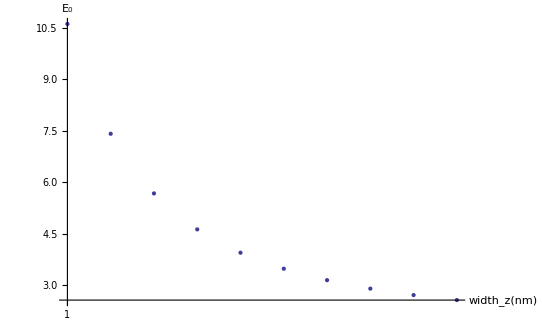

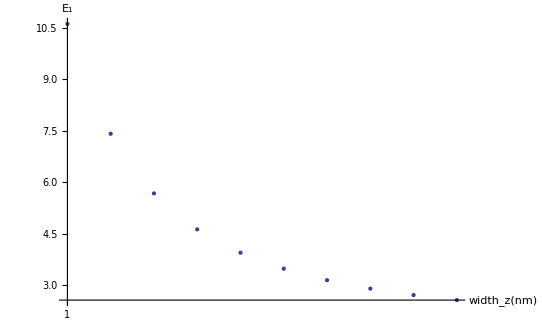

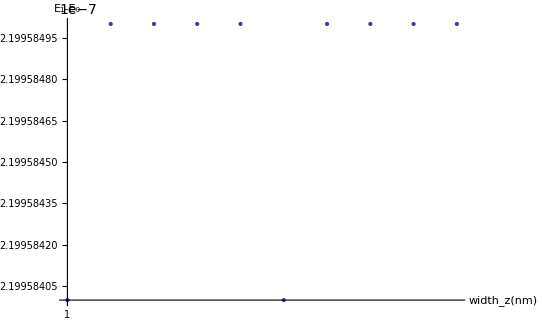

```mathematica
ListPlot[Table[gfactor[[i]][[2]],{i,1,10}],Ticks->{{{1,"1"},{25,"50"},{50,"100"}},Automatic},AxesLabel->{"width_z(nm)","E_0"},PlotRange->All]

ListPlot[Table[gfactor[[i]][[3]],{i,1,10}],Ticks->{{{1,"1"},{25,"50"},{50,"100"}},Automatic},AxesLabel->{"width_z(nm)","E_1"},PlotRange->All]

ListPlot[Table[gfactor[[i]][[4]],{i,1,10}],Ticks->{{{1,"1"},{25,"50"},{50,"100"}},Automatic},AxesLabel->{"width_z(nm)","E_1-E_0"},PlotRange->All]
```

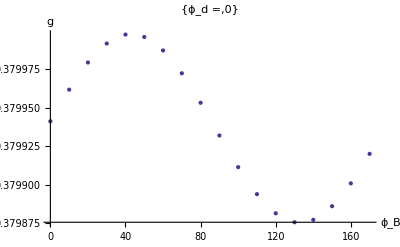
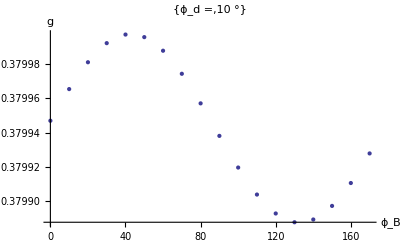
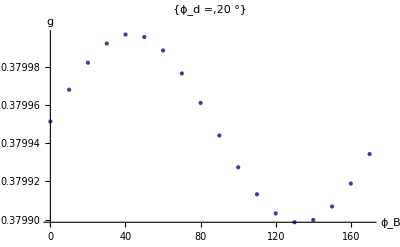
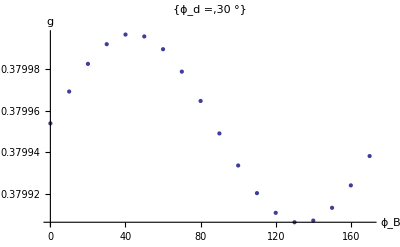
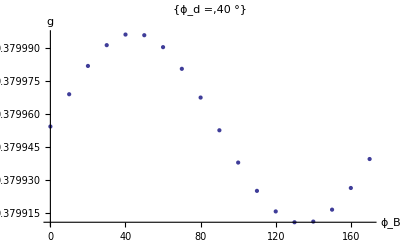
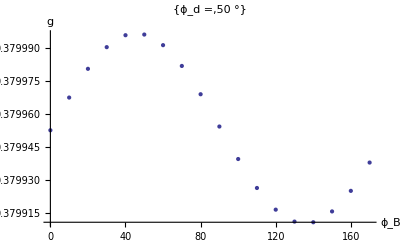
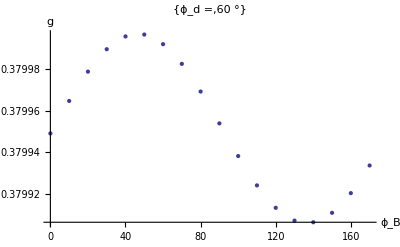
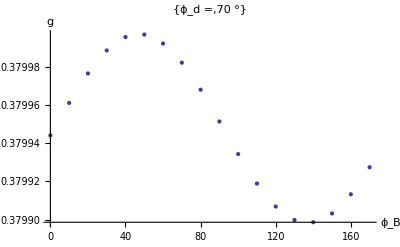

```mathematica
Table[ListPlot[Table[{gfactor[[i]][[1]],gfactor[[i]][[5]]},{i,1+18*j,18+18*j}],AxesLabel->{"ϕ_B","g"},PlotLabel->{"ϕ_d =",j*10 "°"}],{j,0,17}]
```

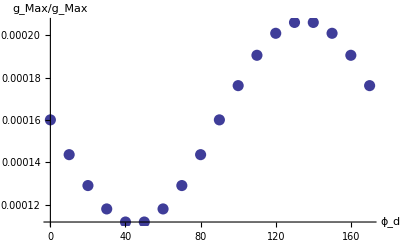

```mathematica
ListPlot[Table[{j*10,(Max[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]]-Min[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]])/(Max[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]]+Min[Table[gfactor[[i]][[5]],{i,1+18*j,18+18*j}]])},{j,0,17}],AxesLabel->{"ϕ_d","g_Max/g_Max"},PlotStyle->Directive[PointSize->0.02]]
```